```mathematica
ClearAll["Global`*"]
<< HPL`;
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

ToFileName::strse: A string or list of strings is expected at position 1 in ToFileName[{$HPLPath},MinimalSet2.m].

FileType::badfile: The specified argument, ToFileName[{$HPLPath},MinimalSet2.m], should be a valid string or File object.

ToFileName::strse: A string or list of strings is expected at position 1 in ToFileName[{$HPLPath},MinimalSet3.m].

FileType::badfile: The specified argument, ToFileName[{$HPLPath},MinimalSet3.m], should be a valid string or File object.

ToFileName::strse: A string or list of strings is expected at position 1 in ToFileName[{$HPLPath},MinimalSet4.m].

General::stop: Further output of ToFileName::strse will be suppressed during this calculation.

FileType::badfile: The specified argument, ToFileName[{$HPLPath},MinimalSet4.m], should be a valid string or File object.

General::stop: Further output of FileType::badfile will be suppressed during this calculation.

StringTake::take: Cannot take positions 1 through -3 in "".

StringJoin::string: String expected at position 2 in Rules for minimal set loaded for weights: <>StringTake[,{1,-3}]<>..

Rules for minimal set loaded for weights: <>StringTake[,{1,-3}]<>.

StringTake::take: Cannot take positions 1 through -3 in "".

StringJoin::string: String expected at position 2 in Rules for minimal set for + - weights loaded for weights: <>StringTake[,{1,-3}]<>..

Rules for minimal set for + - weights loaded for weights: <>StringTake[,{1,-3}]<>.

Table of MZVs loaded up to weight Null

Table of values at I loaded up to weight Null

Get::stream: ToFileName[{$HPLPath},nmzv.m] is not a string, SocketObject, InputStream[ ] or OutputStream[ ].

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

Extract equations (B.5) - (B.7) from [Vogt, Moch: “The third-order QCD corrections to deep-inelastic scattering by photon exchange” ,Nucl. Phys. B, 724 (1-2), 3, 2005] with the help of ChatGPT

```mathematica
pqq[x_]:=2/(1-x)-1-x;
pqg[x_]:=1-2 x+2 x^2;
pgq[x_]:=2/x-2+x;
pgg[x_]:=1/(1-x)+1/x-2+x-x^2;

c2ns2[x_]:=CF*(CF-CA/2)*((8/5)*(9*pqg[-x]*(1-x)+pgq[-x]*(1-x^-1)+(37+17*x))*HPL[{-1,0},x]+4*pqq[-x]*(7*Zeta3+6*HPL[{-2,0},x]+4*HPL[{-1,2},x]-8*HPL[{-1,-1,0},x]+10*HPL[{-1,0,0},x]-3*HPL[{0,0,0},x]-8*HPL[{-1},x]*Zeta2-2*HPL[{0},x]+2*HPL[{0},x]*Zeta2-2*HPL[{3},x])-(72/5)*pqg[x]*((1+x)*(Zeta2-HPL[{0,0},x])-1-HPL[{0},x])+(8/5)*pgq[x]*(1-HPL[{0},x])+8*(1-5*x)*(HPL[{1,0,0},x]-HPL[{1},x]*Zeta2)-8*(1+5*x)*(2*HPL[{-1,-1,0},x]-HPL[{-1,0,0},x]+HPL[{-1},x]*Zeta2))+CF*nf*(1/54*pqq[x]*(247-144*Zeta2+180*HPL[{0,0},x]+72*HPL[{1,0},x]+72*HPL[{1,1},x]+342*HPL[{0},x]+174*HPL[{1},x]+144*HPL[{2},x])-1/3*(7+19*x)*HPL[{0},x]-1/3*(1+13*x)*HPL[{1},x]-1/18*(23+243*x)+DiracDelta[1-x]*(457/36+4/3*Zeta3+38/3*Zeta2))+CF^2*(16*HPL[{-2,0},x]+1/5*(33+37*x)*HPL[{0,0},x]+1/4*pqq[x]*(51+128*Zeta3+48*Zeta2+96*HPL[{-2,0},x]-12*HPL[{0,0},x]-72*HPL[{1,0},x]-72*HPL[{1,1},x]-96*HPL[{1,2},x]-96*HPL[{2,0},x]-112*HPL[{2,1},x]-32*HPL[{0,0,0},x]-48*HPL[{1,0,0},x]-128*HPL[{1,1,0},x]-96*HPL[{1,1,1},x]+122*HPL[{0},x]+96*HPL[{0},x]*Zeta2+54*HPL[{1},x]+32*HPL[{1},x]*Zeta2-48*HPL[{2},x]-96*HPL[{3},x])-1/2*(43+63*x)*HPL[{0},x]+1/2*(59-109*x)*HPL[{1},x]-4*(1-19*x)*Zeta3+2*(1+x)*(7*HPL[{1,0},x]+2*HPL[{2,0},x]+2*HPL[{2,1},x]+5*HPL[{0,0,0},x]-4*HPL[{0},x]*Zeta2+4*HPL[{3},x])+2*(5+9*x)*(HPL[{1,1},x]+2*HPL[{2},x])-4/5*(7+13*x)*Zeta2-1/4*(93+209*x)+DiracDelta[1-x]*(331/8-78*Zeta3+69*Zeta2+6*Zeta2^2))+CA*CF*(-1/108*pqq[x]*(3155-216*Zeta3-1584*Zeta2+1296*HPL[{-2,0},x]+1980*HPL[{0,0},x]+792*HPL[{1,0},x]+792*HPL[{1,1},x]+432*HPL[{1,2},x]+648*HPL[{0,0,0},x]+864*HPL[{1,0,0},x]-432*HPL[{1,1,0},x]+4302*HPL[{0},x]-432*HPL[{0},x]*Zeta2+2202*HPL[{1},x]-1296*HPL[{1},x]*Zeta2+1584*HPL[{2},x]+432*HPL[{3},x])+1/6*(71+323*x)*HPL[{0},x]-17/6*(5-19*x)*HPL[{1},x]-4/5*(9+16*x)*(Zeta2-HPL[{0,0},x])+1/36*(139+3159*x)-8*(5*Zeta3*x+HPL[{-2,0},x])-DiracDelta[1-x]*(5465/72-140/3*Zeta3+251/3*Zeta2-71/5*Zeta2^2));

c2ps2[x_]:=Module[{},CF*(8/3*(-pqg[-x]+pgq[-x])*HPL[{-1,0},x]+8/27*pqg[x]*(28+27*Zeta2-36*HPL[{0,0},x]-9*HPL[{1,0},x]-9*HPL[{1,1},x]-24*HPL[{0},x]+6*HPL[{1},x]-27*HPL[{2},x])+4/27*pgq[x]*(43-18*Zeta2+18*HPL[{1,0},x]+18*HPL[{1,1},x]-39*HPL[{1},x])+8/9*(71-49*x)*HPL[{0},x]+4/3*(16-13*x)*HPL[{1},x]+8*(1-2*x)*HPL[{2},x]+12*(1-x)*(HPL[{1,0},x]+HPL[{1,1},x])-2/3*(1+x)*(12*Zeta3+12*HPL[{-1,0},x]-13*HPL[{0,0},x]-12*HPL[{2,0},x]-12*HPL[{2,1},x]-30*HPL[{0,0,0},x]+24*HPL[{0},x]*Zeta2-24*HPL[{3},x])+22/3*(3-5*x)-8/3*(5-x)*Zeta2)
];


c2g2[x_]:=Module[{},CF*((4/15)*(pgq[-x]*(1-x^-1)+(217+117*x))*HPL[{-1,0},x]+1/15*(639-1004*x)*HPL[{0,0},x]-(8/5)*pqg[-x]*(6*(1-x)*HPL[{-1,0},x]-5*(2*HPL[{-2,0},x]-2*HPL[{-1,-1,0},x]+HPL[{-1,0,0},x]-HPL[{-1},x]*Zeta2))+(2/5)*pqg[x]*(6*(19+4*x)*(Zeta2-HPL[{0,0},x])-(9-90*Zeta3+90*HPL[{1,0},x]+90*HPL[{1,1},x]+60*HPL[{1,2},x]+40*HPL[{2,0},x]+50*HPL[{2,1},x]+50*HPL[{0,0,0},x]+30*HPL[{1,0,0},x]+40*HPL[{1,1,0},x]+50*HPL[{1,1,1},x]+54*HPL[{0},x]-60*HPL[{0},x]*Zeta2+30*HPL[{1},x]-40*HPL[{1},x]*Zeta2+90*HPL[{2},x]+60*HPL[{3},x]))+(4/15)*pgq[x]*(1-HPL[{0},x])+1/3*(16-61*x)*HPL[{0},x]-2*(1-8*x)*HPL[{1},x]+4*(5-4*x)*HPL[{2},x]-4*(1-18*x)*Zeta3+2*(1-2*x)*(8*HPL[{-2,0},x]+2*HPL[{2,0},x]+2*HPL[{2,1},x]+5*HPL[{0,0,0},x]+4*HPL[{1,0,0},x]-4*HPL[{0},x]*Zeta2-4*HPL[{1},x]*Zeta2+4*HPL[{3},x])-8*(1+2*x)*(2*HPL[{-1,-1,0},x]-HPL[{-1,0,0},x]+HPL[{-1},x]*Zeta2)+2*(5+4*x)*(HPL[{1,0},x]+HPL[{1,1},x])-(4/15)*(111-176*x)*Zeta2-1/3*(117-121*x))+CA*((8/3)*(pgq[-x]-3*(4+3*x))*HPL[{-1,0},x]+(4/3)*HPL[{0,0},x]*(47+35*x)+2*(23-6*x)*HPL[{1,0},x]+6*(7-2*x)*HPL[{1,1},x]+4*(5+14*x)*HPL[{0,0,0},x]+(4/3)*pqg[-x]*(6*HPL[{-2,0},x]+10*HPL[{-1,0},x]+6*HPL[{-1,2},x]+9*HPL[{-1,0,0},x]-6*HPL[{-1},x]*Zeta2)-1/54*pqg[x]*(4493-648*Zeta3-3996*Zeta2+3492*HPL[{0,0},x]+2412*HPL[{1,0},x]+2196*HPL[{1,1},x]+216*HPL[{1,2},x]+432*HPL[{2,0},x]+432*HPL[{2,1},x]+432*HPL[{1,0,0},x]+648*HPL[{1,1,0},x]+216*HPL[{1,1,1},x]+6270*HPL[{0},x]-432*HPL[{0},x]*Zeta2+4710*HPL[{1},x]-216*HPL[{1},x]*Zeta2+3996*HPL[{2},x]+432*HPL[{3},x])+(4/27)*pgq[x]*(43-18*Zeta2+18*HPL[{1,0},x]+18*HPL[{1,1},x]-39*HPL[{1},x])+1/9*(1567-338*x)*HPL[{0},x]+1/3*(289-52*x)*HPL[{1},x]+2*(33-2*x)*HPL[{2},x]-4*(1-2*x)*(HPL[{1,0,0},x]-HPL[{1},x]*Zeta2)-4*(1+2*x)*(2*HPL[{-2,0},x]-2*HPL[{-1,-1,0},x]+HPL[{-1,0,0},x]-HPL[{-1},x]*Zeta2)-8*(1+3*x)*(Zeta3+2*HPL[{0},x]*Zeta2-2*HPL[{3},x])+8*(1+4*x)*(HPL[{2,0},x]+HPL[{2,1},x])+7/6*(105-46*x)-2/3*(107-10*x)*Zeta2)];
```

Compare to equations (4.8) - (4.10) from the same paper.

```mathematica
L0[x]:=Log[x];
L1[x]:=Log[1-x];
D0[x]:=1/(1-x);
D1[x]:=L1[x]/(1-x);
D2[x]:=L1[x]^2/(1-x);
D3[x]:=L1[x]^3/(1-x);

c2ns2appr[x_]=Module[{},
128/9*D3[x]-184/3*D2[x]-31.1052*D1[x]+188.641*D0[x]-338.513*DiracDelta[1-x]
-17.74*L1[x]^3+72.24*L1[x]^2-628.8*L1[x]-181.0-806.7*x+0.719*x*L0[x]^4
+L0[x]*L1[x]*(37.75*L0[x]-147.1*L1[x])-28.384*L0[x]-20.70*L0[x]^2-80/27*L0[x]^3
+nf*(
16/9*D2[x]-232/27*D1[x]+6.34888*D0[x]+46.8531*DiracDelta[1-x]-1.500*L1[x]^2
+24.87*L1[x]-7.8109-17.82*x-12.97*x^2-0.185*x*L0[x]^3+8.113*L0[x]*L1[x]
+16/3*L0[x]+20/9*L0[x]^2
)
];

c2ns2regappr[x_]=Module[{},
-17.74*L1[x]^3+72.24*L1[x]^2-628.8*L1[x]-181.0-806.7*x+0.719*x*L0[x]^4
+L0[x]*L1[x]*(37.75*L0[x]-147.1*L1[x])-28.384*L0[x]-20.70*L0[x]^2-80/27*L0[x]^3
+nf*(
-1.500*L1[x]^2
+24.87*L1[x]-7.8109-17.82*x-12.97*x^2-0.185*x*L0[x]^3+8.113*L0[x]*L1[x]
+16/3*L0[x]+20/9*L0[x]^2
)
];

c2ns2plusappr[x_]=Module[{},
128/9*D3[x]-184/3*D2[x]-31.1052*D1[x]+188.641*D0[x]
+nf*(
16/9*D2[x]-232/27*D1[x]+6.34888*D0[x]
)
];

c2ns2localappr[x_]=Module[{},
-338.513*DiracDelta[1-x]
+nf*(
46.8531*DiracDelta[1-x]
)
];

c2g2appr[x_]=Module[{},
58/9*L1[x]^3-24*L1[x]^2-34.88*L1[x]+30.586-(25.08+760.3*x
+29.65*L1[x]^3)*(1-x)+1204*x*L0[x]^2+L0[x]*L1[x]*(293.8+711.2*x+1043*L0[x])
+115.6*L0[x]-7.109*L0[x]^2+70/9*L0[x]^3+11.9033*(1-x)/x
];

c2ps2appr[x_]=Module[{},
(8/3*L1[x]^2-32/3*L1[x]+9.8937)*(1-x)+(9.57-13.41*x+0.08*L1[x]^3)*(1-x)^2
+5.667*x*L0[x]^3-L0[x]^2*L1[x]*(20.26-33.93*x)+43.36*(1-x)*L0[x]-1.053*L0[x]^2
+40/9*L0[x]^3+5.2903*(1-x)^2/x
];
```

The old parametrizations from [van Neerven, Vogt; Nucl. Phys. B. 568 (1-2), 263, 2000] eq. 3.2 and [van Neerven, Vogt; Nucl. Phys. B. 588 (1), 345, 2000] eq. 3.4, 3.6 is here...

```mathematica
c2ns2approld[x_]=Module[{},
14.2222* D3[x]−61.3333 *D2[x]−31.105 *D1[x]+188.64*D0[x]
−17.19 *L1[x]^3+71.08*L1[x]^2−660.7 *L1[x]+L1[x]*L0[x]*(−174.8 *L1[x]+95.09 *L0[x])
−2.835 *L0[x]^3−17.08 *L0[x]^2 +5.986 *L0[x]−1008* x−69.59−338.046 *DiracDelta[1−x]+
nf*(
1.77778 *D2[x]−8.5926 *D1[x]+6.3489*D0[x]
−1.707 *L1[x]^2+22.95 *L1[x]+L1[x]*L0[x](3.036 *L0[x]+17.97) 
+2.244 *L0[x]^2+5.770* L0[x]−37.91* x−5.691+46.8405 *DiracDelta[1-x]
)
];

c2ps2approld[x_]=Module[{},
-0.101*(1-x)*L1[x]^3-(24.75-13.80*x)*L1[x]*L0[x]^2+30.23*L1[x]*L0[x]
+4.310*L0[x]^3-2.086*L0[x]^2+39.78*L0[x]+5.290*(1/x-1)
];

c2g2approld[x_]=Module[{},
(6.445+209.4*(1-x))*L1[x]^3-24.00*L1[x]^2+(1494/x-1483)*L1[x]
+L1[x]*L0[x]*(-871.8*L1[x]-724.1*L0[x])+5.319*L0[x]^3-59.48*L0[x]^2-284.8*L0[x]
+11.90/x+392.4-0.28*DiracDelta[1-x]
];
```

First, check whether the parametrizations match

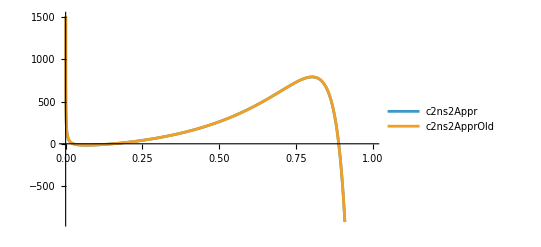

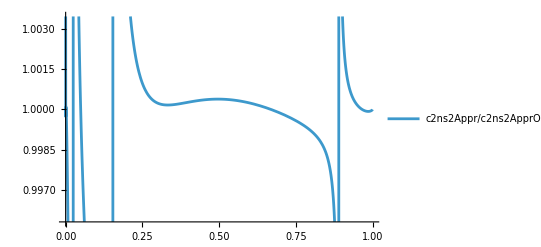

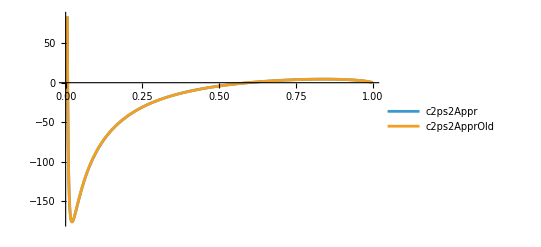

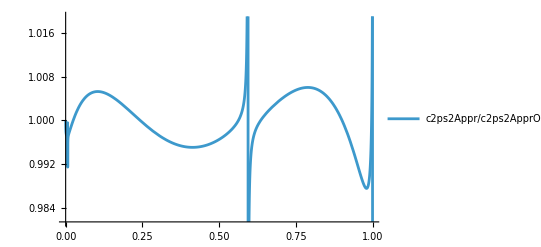

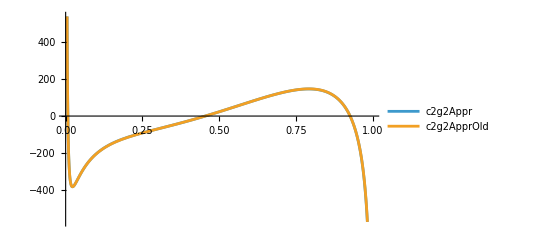

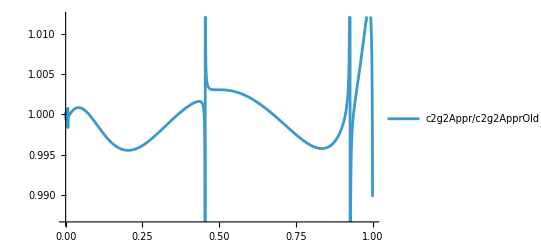

```mathematica
Plot[{
c2ns2appr[x]/.nf->3,
c2ns2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ns2Appr","c2ns2ApprOld"}]
Plot[{
c2ns2appr[x]/c2ns2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ns2Appr/c2ns2ApprOld"}]
Plot[{
c2ps2appr[x]/.nf->3,
c2ps2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ps2Appr","c2ps2ApprOld"}]
Plot[{
c2ps2appr[x]/c2ps2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ps2Appr/c2ps2ApprOld"}]
Plot[{
c2g2appr[x]/.nf->3,
c2g2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2g2Appr","c2g2ApprOld"}]
Plot[{
c2g2appr[x]/c2g2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2g2Appr/c2g2ApprOld"}]
```

If the parametrization coincide, then we are discussing the correct objects and there are probably no mismatches in notation etc. 

Now, let us check whether exact formula and (new) parametrization coincide...

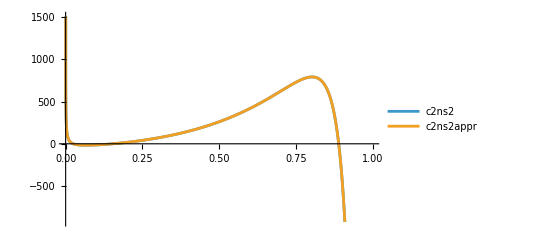

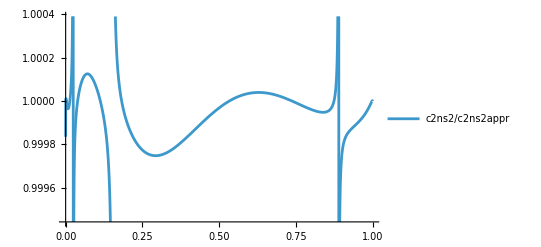

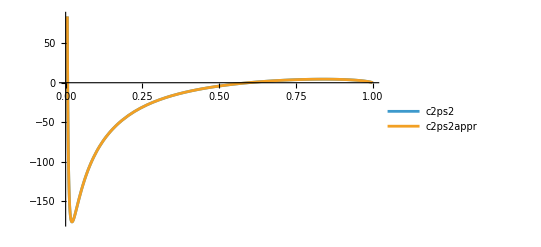

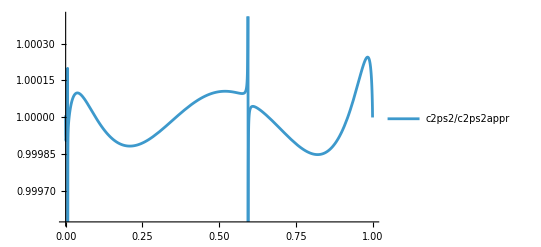

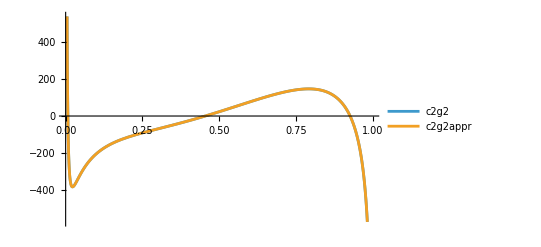

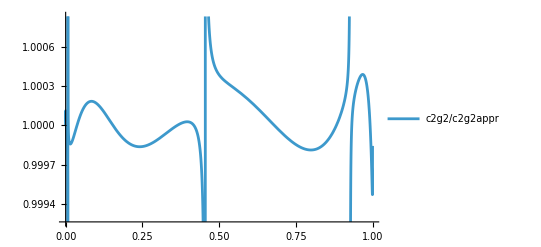

```mathematica
Plot[{
c2ns2[x]/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2ns2appr[x]/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2ns2","c2ns2appr"}]
Plot[
(c2ns2[x]/c2ns2appr[x])/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2ns2/c2ns2appr"}]
Plot[{
c2ps2[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2ps2appr[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2ps2","c2ps2appr"}]
Plot[
(c2ps2[x]/c2ps2appr[x])/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2ps2/c2ps2appr"}]
Plot[{
c2g2[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2g2appr[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2g2","c2g2appr"}]
Plot[
(c2g2[x]/c2g2appr[x])/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2g2/c2g2appr"}]
```

This seems to match more or less.

Now let us rewrite the coefficient functions in a way that we can put into the C++ program.
We split the functions into Plus/Local/Regular part and format everything accordingly.

```mathematica
HPLreplace={
HPL[a_List,x_]:>myHPL[HPLMtoA[a],x],
myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]]
};

codereplacements={
"Zeta2"->"MATH::ZETA2",
"Zeta3"->"MATH::ZETA3",
"nf"->"\nQCD::NF",
"CF"->"\nQCD::CF",
"CA"->"\nQCD::CA",
"Power"->"std::pow",
"\""->"",
RegularExpression["HPL(\\d+)\\(([^)]*)\\)"]:>StringReplace["HPL$1_$2",{","->"","-"->"m"}],
"Log(1 - x)"->"L1x",
"Log(x)"->"L0x",
"Log(1 - z)"->"L1z",
"Log(z)"->"L0z"
};

rationalstring=r_Rational:>ToString[Numerator[r]]<>"./"<>ToString[Denominator[r]]<>".";

foreval={
CA->3,
CF->4/3,
nf->3,
Zeta2->Zeta[2],
Zeta3->Zeta[3]
};
```

@@@c2ns2xlocal=(std::pow(
QCD::CF,2)*(331./8. + 69*MATH::ZETA2 + 6*std::pow(MATH::ZETA2,2) - 78*MATH::ZETA3) + 
QCD::CA*
QCD::CF*(-5465./72. + -251./3.*MATH::ZETA2 + 71./5.*std::pow(MATH::ZETA2,2) + 140./3.*MATH::ZETA3) + 
QCD::CF*
QCD::NF*(457./36. + 38./3.*MATH::ZETA2 + 4./3.*MATH::ZETA3))*DiracDelta(-1 + z)

@@@c2ns2xplus=(
QCD::CA*
QCD::CF*(3155./54. + -44./3.*MATH::ZETA2 - 40*MATH::ZETA3 + (-367./9. + 8*MATH::ZETA2)*L1z + 22./3.*std::pow(L1z,2)) + 
QCD::CF*
QCD::NF*(-247./27. + 8./3.*MATH::ZETA2 + 58./9.*L1z + -4./3.*std::pow(L1z,2)) + std::pow(
QCD::CF,2)*(-51./2. - 36*MATH::ZETA2 + 8*MATH::ZETA3 + (27 + 32*MATH::ZETA2)*L1z + 18*std::pow(L1z,2) - 8*std::pow(L1z,3)))/(-1 + z)

@@@c2ns2xlocalplus=
QCD::CA*
QCD::CF*((-3155./54. + 44./3.*MATH::ZETA2 + 40*MATH::ZETA3)*L1x + (367./18. - 4*MATH::ZETA2)*std::pow(L1x,2) + -22./9.*std::pow(L1x,3)) + 
QCD::CF*
QCD::NF*((247./27. + -8./3.*MATH::ZETA2)*L1x + -29./9.*std::pow(L1x,2) + 4./9.*std::pow(L1x,3)) + std::pow(
QCD::CF,2)*((51./2. + 36*MATH::ZETA2 - 8*MATH::ZETA3)*L1x + (-27./2. - 16*MATH::ZETA2)*std::pow(L1x,2) - 6*std::pow(L1x,3) + 2*std::pow(L1x,4))

@@@c2ns2xreg=
QCD::CA*
QCD::CF*(3709./135. + -8./5./z + 17626./135.*z + -72./5.*std::pow(z,2) + (12 - 56*z)*MATH::ZETA3 + (164./5.*HPL1_0z)/(-1 + std::pow(z,2)) + (-8./5.*HPL1_0z)/(z*(-1 + std::pow(z,2))) + (-118./5.*z*HPL1_0z)/(-1 + std::pow(z,2)) + (799./15.*std::pow(z,2)*HPL1_0z)/(-1 + std::pow(z,2)) + (1693./15.*std::pow(z,3)*HPL1_0z)/(-1 + std::pow(z,2)) + (-72./5.*std::pow(z,4)*HPL1_0z)/(-1 + std::pow(z,2)) + 56./9.*HPL1_1z + 668./9.*z*HPL1_1z + MATH::ZETA2*(-44./3. + -104./3.*z + 72./5.*std::pow(z,3) - (8*z*HPL1_0z)/(-1 + std::pow(z,2)) - (8*std::pow(z,3)*HPL1_0z)/(-1 + std::pow(z,2)) - 8*HPL1_1z - 32*z*HPL1_1z) - 36*HPL2_m10z + (-8./5.*HPL2_m10z)/std::pow(z,2) - 20*z*HPL2_m10z + 72./5.*std::pow(z,3)*HPL2_m10z + 55./3.*HPL2_00z + 115./3.*z*HPL2_00z + -72./5.*std::pow(z,3)*HPL2_00z + 44./3.*HPL2_01z + 44./3.*z*HPL2_01z + 22./3.*HPL2_10z + 22./3.*z*HPL2_10z + 22./3.*HPL2_11z + 22./3.*z*HPL2_11z - 8*HPL3_m1m10z + 56*z*HPL3_m1m10z + 16*HPL3_m100z - 40*z*HPL3_m100z + 8*HPL3_m101z - 8*z*HPL3_m101z + 16*HPL3_0m10z + 12*z*HPL3_000z + 8*z*HPL3_001z + (-28*MATH::ZETA3 + MATH::ZETA2*(20*HPL1_m1z + 24*z*HPL1_m1z + 36*std::pow(z,2)*HPL1_m1z) + 32*HPL3_m1m10z - 40*HPL3_m100z - 16*HPL3_m101z - 24*HPL3_0m10z + 12*HPL3_000z + 8*HPL3_001z)/(1 + z) + 4*HPL3_100z + 28*z*HPL3_100z + 4*HPL3_101z + 4*z*HPL3_101z - 4*HPL3_110z - 4*z*HPL3_110z + (36*MATH::ZETA3 + 367./9.*HPL1_1z + 110./3.*HPL2_00z + 88./3.*HPL2_01z + 44./3.*HPL2_10z + 44./3.*HPL2_11z + 24*HPL3_0m10z + 12*HPL3_000z + 8*HPL3_001z + 16*HPL3_100z + 8*HPL3_101z - 8*HPL3_110z + MATH::ZETA2*(-44./3. - 24*HPL1_1z - 8*L1z) + 367./9.*L1z + -22./3.*std::pow(L1z,2))/(-1 + z)) + 
QCD::CF*
QCD::NF*(-158./27. + -488./27.*z + (8./3. + 8./3.*z)*MATH::ZETA2 - (4*HPL1_0z)/(-1 + std::pow(z,2)) + (-26./3.*std::pow(z,2)*HPL1_0z)/(-1 + std::pow(z,2)) + (-38./3.*std::pow(z,3)*HPL1_0z)/(-1 + std::pow(z,2)) + -32./9.*HPL1_1z + -68./9.*z*HPL1_1z + -10./3.*HPL2_00z + -10./3.*z*HPL2_00z + -8./3.*HPL2_01z + -8./3.*z*HPL2_01z + -4./3.*HPL2_10z + -4./3.*z*HPL2_10z + -4./3.*HPL2_11z + -4./3.*z*HPL2_11z + (8./3.*MATH::ZETA2 + -58./9.*HPL1_1z + -20./3.*HPL2_00z + -16./3.*HPL2_01z + -8./3.*HPL2_10z + -8./3.*HPL2_11z + -58./9.*L1z + 4./3.*std::pow(L1z,2))/(-1 + z)) + std::pow(
QCD::CF,2)*(-124./5. + 16./5./z + -461./5.*z + 144./5.*std::pow(z,2) + (-64 + 72*z)*MATH::ZETA3 + (-93./5.*HPL1_0z)/(-1 + std::pow(z,2)) + (16./5.*HPL1_0z)/(z*(-1 + std::pow(z,2))) + (101./5.*z*HPL1_0z)/(-1 + std::pow(z,2)) + (-276./5.*std::pow(z,2)*HPL1_0z)/(-1 + std::pow(z,2)) + (-502./5.*std::pow(z,3)*HPL1_0z)/(-1 + std::pow(z,2)) + (144./5.*std::pow(z,4)*HPL1_0z)/(-1 + std::pow(z,2)) + 16*HPL1_1z - 68*z*HPL1_1z + MATH::ZETA2*(-32 - 8*z + -144./5.*std::pow(z,3) - (24*HPL1_0z)/(-1 + std::pow(z,2)) - (8*z*HPL1_0z)/(-1 + std::pow(z,2)) - (40*std::pow(z,2)*HPL1_0z)/(-1 + std::pow(z,2)) - (24*std::pow(z,3)*HPL1_0z)/(-1 + std::pow(z,2)) - 16*HPL1_1z + 32*z*HPL1_1z) + 72*HPL2_m10z + (16./5.*HPL2_m10z)/std::pow(z,2) + 40*z*HPL2_m10z + -144./5.*std::pow(z,3)*HPL2_m10z + 24*HPL2_00z - 4*z*HPL2_00z + 144./5.*std::pow(z,3)*HPL2_00z + 32*HPL2_01z + 48*z*HPL2_01z + 32*HPL2_10z + 32*z*HPL2_10z + 28*HPL2_11z + 36*z*HPL2_11z + 16*HPL3_m1m10z - 112*z*HPL3_m1m10z - 32*HPL3_m100z + 80*z*HPL3_m100z - 16*HPL3_m101z + 16*z*HPL3_m101z - 32*HPL3_0m10z + 30*HPL3_000z + 6*z*HPL3_000z + (56*MATH::ZETA3 + MATH::ZETA2*(-40*HPL1_m1z - 48*z*HPL1_m1z - 72*std::pow(z,2)*HPL1_m1z) - 64*HPL3_m1m10z + 80*HPL3_m100z + 32*HPL3_m101z + 48*HPL3_0m10z - 24*HPL3_000z - 16*HPL3_001z)/(1 + z) + 40*HPL3_001z + 24*z*HPL3_001z + 28*HPL3_010z + 28*z*HPL3_010z + 32*HPL3_011z + 32*z*HPL3_011z + 20*HPL3_100z - 28*z*HPL3_100z + 24*HPL3_101z + 24*z*HPL3_101z + 32*HPL3_110z + 32*z*HPL3_110z + 24*HPL3_111z + 24*z*HPL3_111z + (-72*MATH::ZETA3 - 27*HPL1_1z + 6*HPL2_00z + 24*HPL2_01z + 36*HPL2_10z + 36*HPL2_11z - 48*HPL3_0m10z + 16*HPL3_000z + 48*HPL3_001z + 48*HPL3_010z + 56*HPL3_011z + 24*HPL3_100z + 48*HPL3_101z + 64*HPL3_110z + 48*HPL3_111z + MATH::ZETA2*(12 - 16*HPL1_1z - 32*L1z) - 27*L1z - 18*std::pow(L1z,2) + 8*std::pow(L1z,3))/(-1 + z))

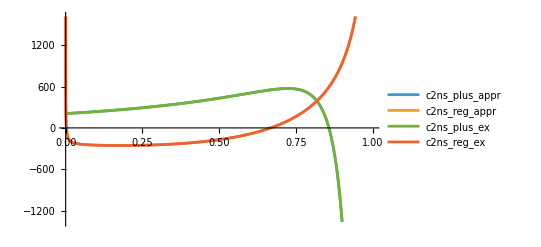

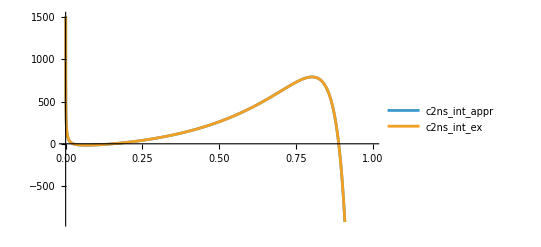

```mathematica
c2ns2x=c2ns2[x];

c2ns2xTerms=List@@Expand[c2ns2x];
c2ns2xlocalTerms=Select[c2ns2xTerms,!FreeQ[#,DiracDelta[1-x]]&];

c2ns2x1oxTerms=Select[c2ns2xTerms,!FreeQ[#,1/(1-x)]&];
c2ns2x1ox=Total@c2ns2x1oxTerms;
c2ns2x1oxSer=Normal@Series[HPLConvertToKnownFunctions@c2ns2x1ox,{x,1,-1}];
c2ns2xplusTerms=Select[List@@Expand[c2ns2x1oxSer],(Exponent[#,1-x]==-1||Exponent[#,-1+x]==-1)&]/.{π^2->6*Zeta2,Zeta[3]->Zeta3};
c2ns2xregTerms=Join[Complement[c2ns2xTerms,c2ns2xlocalTerms],-c2ns2xplusTerms];

c2ns2xlocal=(Total@c2ns2xlocalTerms)//Collect[#,{DiracDelta[1-x],nf,CF,CA,Zeta2,Zeta3}]&;
c2ns2xplus=(Total@c2ns2xplusTerms)//Collect[#,{1/(x-1),nf,CF,CA,_Log,Zeta2,Zeta3}]&;
c2ns2xreg=(Total@c2ns2xregTerms)//Simplify//Expand//Collect[#,{nf,CF,CA,1/(-1+x),1/(1+x),Zeta2,Zeta3}]&;

c2ns2xlocalplus=-Integrate[c2ns2xplus,{x,0,t},Assumptions->{t∈Reals,0<t<1}]/.t->x//Simplify//Expand//Collect[#,{nf,CF,CA,_Log,Zeta2,Zeta3}]&;

Print["@@@c2ns2xlocal="<>StringReplace[ToString[CForm[c2ns2xlocal//.HPLreplace/.x->z]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ns2xplus="<>StringReplace[ToString[CForm[c2ns2xplus//.HPLreplace/.x->z]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ns2xlocalplus="<>StringReplace[ToString[CForm[c2ns2xlocalplus]/.rationalstring,InputForm],codereplacements]]
Print["@@@c2ns2xreg="<>StringReplace[ToString[CForm[c2ns2xreg//.HPLreplace/.x->z]/.rationalstring,InputForm],codereplacements]]


Plot[{
c2ns2plusappr[x]/.foreval,
c2ns2regappr[x]/.foreval,
c2ns2xplus/.foreval,
c2ns2xreg/.foreval
},{x,0,1},PlotLegends->{"c2ns_plus_appr","c2ns_reg_appr","c2ns_plus_ex","c2ns_reg_ex"}]
Plot[{
(c2ns2plusappr[x]+c2ns2regappr[x])/.foreval,
(c2ns2xplus+c2ns2xreg)/.foreval
},{x,0,1},PlotLegends->{"c2ns_int_appr","c2ns_int_ex"}]
```

```mathematica
c2ns2xplus
```

1/(-1+x)(CF nf (-247/27-(4 π^2)/9+(16 Zeta2)/3+58/9 Log[1-x]-4/3 Log[1-x]^2)+CA CF (3155/54+(22 π^2)/9-(88 Zeta2)/3-4 Zeta3+(-367/9-(8 π^2)/3+24 Zeta2) Log[1-x]+22/3 Log[1-x]^2-36 Zeta[3])+CF^2 (-51/2-2 π^2-24 Zeta2-64 Zeta3+(27+(8 π^2)/3+16 Zeta2) Log[1-x]+18 Log[1-x]^2-8 Log[1-x]^3+72 Zeta[3]))

Apparently this integration rule does not work if the pattern does not match exactly (e.g. for 1/(1-x)*a*HPL[{...},x])
So we implement the integration rule by hand, using

∫_0^x f_a(z)HPL(a_1,a_2,...;z)ⅆz=HPL(a,a_1,a_2,...;x)   and   f_1(z)=1/(1-z)

Remember, we actually need “-“ this integral when integrating the plus distribution from x to 1 instead of 0 to 1.

```mathematica
(*
c2ns2plus/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]]/.x->z
c2ns2plusInt=-(1-x)*c2ns2plus/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n+1]][1,Sequence@@a,x]]//FullSimplify
CForm[Collect[c2ns2plusInt,{nf,CF,CA}]]
*)
```